```mathematica
g=9.8;
T0=0; T=0.06;
xmax=1; xmin=0; n=100;
dx=(xmax-xmin)/n;
(*dt=0.01;*)
xmesh=Table[x,{x,xmin,xmax,dx }];
h=Table[2,n/2]~Join~Table[1,n/2];
u=Table[0,n];
Q={h,h*u};
u=Q[[2]]/Q[[1]];
h=Q[[1]];
F={h*u,h*u^2+1/2*g*h^2};
dt=0.5*Min[dx/Max[(Sqrt[g*h]+u),(-Sqrt[g*h]+u)]]
Q[[1,5]]
Max[Q[[1]]]
MatrixForm[Q]
MatrixForm[F]
```

0.00112938

2

2

(2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 19.6 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9 | 4.9)

```mathematica
For[t=T0,t<=T,t=t+dt,
(*For[j=0,j<=3,j=j+1,*)
{
dt=0.5*Min[dx/Max[(Sqrt[g*h]+u),(-Sqrt[g*h]+u)]];
(*Создание виртуальных ячеек - твердая стенка*)
Q=Transpose[Insert[Transpose[Q],{ Q[[1,1]],-Q[[2,1]]},1]];
Q=Transpose[Insert[Transpose[Q],{ Q[[1,n]],-Q[[2,n]]},n]];
F=Transpose[Insert[Transpose[F],{ -F[[1,1]],F[[2,1]]},1]];
F=Transpose[Insert[Transpose[F],{ -F[[1,n]],F[[2,n]]},n]];
FF=Table[0,{a,2},{b,n+1}];
(*Проход по ячейкам, нахождение F*)
For[i=1,i<=n+1,i++,
{
SR=Max[N[Q[[2,i]]/Q[[1,i]]+Sqrt[g*Q[[1,i]]]], N[Q[[2,i+1]]/Q[[1,i+1]]+Sqrt[g*Q[[1,i+1]]]]];
SL=Min[N[Q[[2,i]]/Q[[1,i]]-Sqrt[g*Q[[1,i]]]], N[Q[[2,i+1]]/Q[[1,i+1]]-Sqrt[g*Q[[1,i+1]]]]];
(*Print[SL, SR];*)
If[SL>0,FF[[All,i]]=F[[All,i]],
If[SR<0,FF[[All,i]]=F[[All,i+1]],
FF[[All,i]]=N[SR*F[[All,i]]-SL*F[[All,i+1]]+SL*SR*(Q[[All,i+1]]-Q[[All,i]])]/(SR-SL);
]];
}];
(*Вычисление нового слоя*)
Q=N[Transpose[Transpose[Q][[2;;n+1]]-dt/dx*(Transpose[FF][[2;;n+1]]-Transpose[FF][[1;;n]])]];

(*Удаление виртуальных ячеек*)
(*FF=Transpose[Delete[Transpose[F],1]];
FF=Transpose[Delete[Transpose[F],n+1]];*)
u=Q[[2]]/Q[[1]];
h=Q[[1]];
F={h*u,h*u^2+1/2*g*h^2}
(*Print[MatrixForm[Q]];
Print[MatrixForm[FF]];*)
}
]
```

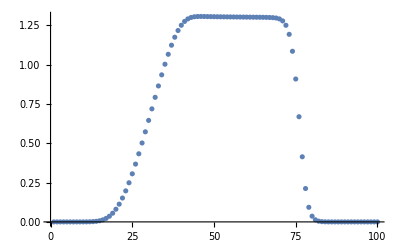

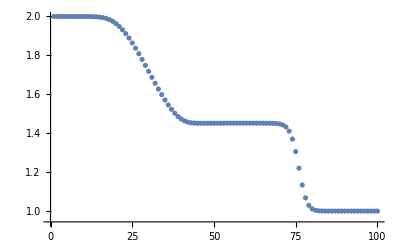

```mathematica
ListPlot[u]
ListPlot[h]
```